# Computational X-plorations

## Literature

## Outline

### Shakespeare’s Romeo and Juliet

Computational Information from Wolfram|Alpha®

### Computational Analysis of Text

Evolution of Topics in Romeo and Juliet

### Sentiment Analysis of Text

Changes in Mood through the Play

### Importing and Visualizing Data

Shakespeare’s Plays: Publishers and Timeline

### Using Data from the Wolfram Data Repository™

Text Analysis of Shakespeare’s Sonnets

## Shakespeare's Romeo and Juliet

### From Wolfram|Alpha

If you type “Romeo and Juliet” as Wolfram|Alpha input, you already get a lot of information:

Romeo and Juliet

WolframAlphaQueryResults

## Computational Analysis of Text

### Evolution of Topics in Romeo and Juliet

The text of the play can be analyzed to visualize how the dramatic development of events propagates through the play.

Import the text of the play:

```mathematica
romeojuliet=Import["http://shakespeare.mit.edu/romeo_juliet/full.html"];
```

Locate the occurrence of the word “Romeo” occur in a sentence:

```mathematica
StringPosition["O Romeo, Romeo, wherefore art thou Romeo?","Romeo"]
```

{{3,7},{10,14},{36,40}}

Find the position of occurrences of given words within the entire text:

```mathematica
mentionsOfRomeo =StringPosition[romeojuliet,"Romeo", IgnoreCase->True]
```

Create a Histogram of occurrences of the word along the body of text:

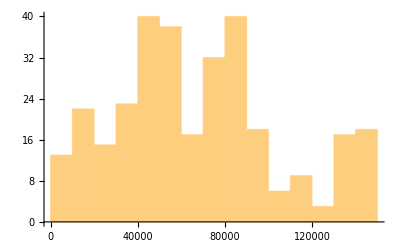

```mathematica
Histogram[mentionsOfRomeo[[All,1]],{10000}]
```

Create a SmoothHistogram showing how often the word occurs as the play progresses:

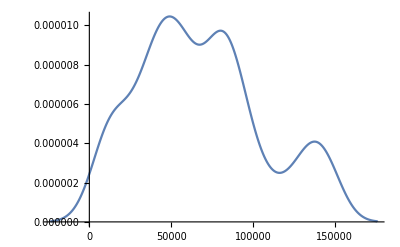

```mathematica
SmoothHistogram[mentionsOfRomeo[[All,1]]]
```

Visualize the occurrence of the words “life” and “death” along with “Romeo” and “Juliet”:

```mathematica
mentions = StringPosition[romeojuliet,#, IgnoreCase->True][[All,1]]&/@ {"romeo","juliet","life","death"};
```

```mathematica
SmoothHistogram[mentions,PlotLegends->{"romeo","juliet","life","death"},]
```

-Graphics-

Visualize the occurrence of the words “love” and “hate” along with “Romeo” and “Juliet”:

```mathematica
SmoothHistogram[StringPosition[romeojuliet,#, IgnoreCase->True][[All,1]]&/@ {"romeo","juliet","love","hate"},PlotLegends->{"romeo","juliet","love","hate"},]
```

-Graphics-

## Sentiment Analysis of Text

Machine learning can be used to detect the sentiment or affective state of each sentence in the text and use it visualize the change in the mood of the play.

This sentiment classifier assumes each sentence conveys only one sentiment. The probabilities reflect the belief in these sentiments, not the proportion of sentiments.

### Changes in Mood through the Play

Extract sentences from the text:

```mathematica
sentences = TextCases[romeojuliet,"Sentence"];
```

Classify the sentiment of each sentence and list the probability of it being “Positive”:

```mathematica
sentiments = Classify["Sentiment",sentences,"Probability"->"Positive"];
```

Visualize the sentiment as the play progresses:

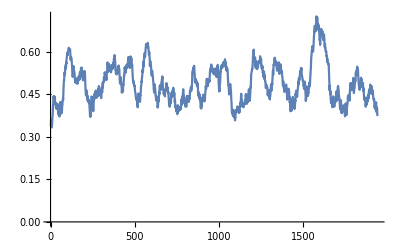

```mathematica
ListLinePlot[MovingAverage[sentiments,50]]
```

## Importing and Visualizing Data

### Shakespeare’s Plays: Publishers and Timeline

Import the data file:

```mathematica
shakespeareData = Import["shakespeare.csv"];
```

Check out the first row:

```mathematica
shakespeareData[[1]]
```

{1623,Julius Caesar,Edward Blount and William & Isaac Jaggard}

Look at all the publishers:

```mathematica
shakespeareData[[All,3]]
```

{Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Thomas Fisher,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Nicholas Ling,Andrew Wise,Missing["NotAvailable"],Andrew Wise and William Aspley,Thomas Walkley,Andrew Wise,Cuthbert Burby,Thomas Thorpe,Thomas Hayes,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Valentine Simmes,Edward Blount and William & Isaac Jaggard,Cuthbert Burby,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Thomas Millington,Thomas Millington,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Henry Gosson,Andrew Wise,Edward Blount and William & Isaac Jaggard,Missing["NotApplicable"],Edward Blount and William & Isaac Jaggard,John Waterson,Edward Blount and William & Isaac Jaggard,Edward Blount and William & Isaac Jaggard,Thomas Millington and Edward White,Richard Bonian and Henry Walley,Richard Field and John Harrison}

Count the number of plays published by each publisher:

```mathematica
publishers =Counts[shakespeareData[[All,3]]]
```

<|Edward Blount and William & Isaac Jaggard→19,Thomas Fisher→1,Nicholas Ling→1,Andrew Wise→3,Missing["NotAvailable"]→1,Andrew Wise and William Aspley→1,Thomas Walkley→1,Cuthbert Burby→2,Thomas Thorpe→1,Thomas Hayes→1,Valentine Simmes→1,Thomas Millington→2,Henry Gosson→1,Missing["NotApplicable"]→1,John Waterson→1,Thomas Millington and Edward White→1,Richard Bonian and Henry Walley→1,Richard Field and John Harrison→1|>

Visualize the counts:

```mathematica
PieChart[publishers]
```

-Graphics-

Add legends and color styling:

```mathematica
PieChart[publishers,ChartLegends->Automatic, ChartStyle->"LightTemperatureMap"]
```

-Graphics-

Look at all the publication dates:

```mathematica
shakespeareData[[All,1]]
```

{1623,1623,1600,1623,1623,1604,1598,1608,1600,1622,1597,1599,1609,1600,1623,1623,1623,1623,1600,1623,1598,1623,1623,1623,1623,1594,1595,1623,1623,1609,1597,1623,1602,1623,1634,1623,1623,1594,1609,1594}

Convert them into date objects:

```mathematica
years =DateObject[{#}]&/@shakespeareData[[All,1]]
```

{Year: 1623,Year: 1623,Year: 1600,Year: 1623,Year: 1623,Year: 1604,Year: 1598,Year: 1608,Year: 1600,Year: 1622,Year: 1597,Year: 1599,Year: 1609,Year: 1600,Year: 1623,Year: 1623,Year: 1623,Year: 1623,Year: 1600,Year: 1623,Year: 1598,Year: 1623,Year: 1623,Year: 1623,Year: 1623,Year: 1594,Year: 1595,Year: 1623,Year: 1623,Year: 1609,Year: 1597,Year: 1623,Year: 1602,Year: 1623,Year: 1634,Year: 1623,Year: 1623,Year: 1594,Year: 1609,Year: 1594}

Look at all the titles:

```mathematica
plays = shakespeareData[[All,2]]
```

{Julius Caesar,Macbeth,A Midsummer Night's Dream,Antony and Cleopatra,As You Like It,Hamlet,Henry IV, Part I,King Lear,Much Ado About Nothing,Othello,Richard III,Romeo and Juliet,Sonnets,The Merchant of Venice,The Taming of the Shrew,The Tempest,Twelfth Night,Coriolanus,Henry IV, Part II,Henry V,Love's Labour's Lost,Cymbeline,All's Well That Ends Well,Henry VIII,Henry VI, Part I,Henry VI, Part II,Henry VI, Part III,The Life and Death of King John,Measure for Measure,Pericles, Prince of Tyre,Richard II,The Comedy of Errors,The Merry Wives of Windsor,The Two Gentlemen of Verona,The Two Noble Kinsmen,The Winter's Tale,Timon of Athens,Titus Andronicus,Troilus and Cressida,The Rape of Lucrece}

Label each date with the corresponding title:

```mathematica
dateAndTitles =MapThread[Labeled[#1,#2]&,{years,plays}]
```

{Year: 1623Julius Caesar,Year: 1623Macbeth,Year: 1600A Midsummer Night's Dream,Year: 1623Antony and Cleopatra,Year: 1623As You Like It,Year: 1604Hamlet,Year: 1598Henry IV, Part I,Year: 1608King Lear,Year: 1600Much Ado About Nothing,Year: 1622Othello,Year: 1597Richard III,Year: 1599Romeo and Juliet,Year: 1609Sonnets,Year: 1600The Merchant of Venice,Year: 1623The Taming of the Shrew,Year: 1623The Tempest,Year: 1623Twelfth Night,Year: 1623Coriolanus,Year: 1600Henry IV, Part II,Year: 1623Henry V,Year: 1598Love's Labour's Lost,Year: 1623Cymbeline,Year: 1623All's Well That Ends Well,Year: 1623Henry VIII,Year: 1623Henry VI, Part I,Year: 1594Henry VI, Part II,Year: 1595Henry VI, Part III,Year: 1623The Life and Death of King John,Year: 1623Measure for Measure,Year: 1609Pericles, Prince of Tyre,Year: 1597Richard II,Year: 1623The Comedy of Errors,Year: 1602The Merry Wives of Windsor,Year: 1623The Two Gentlemen of Verona,Year: 1634The Two Noble Kinsmen,Year: 1623The Winter's Tale,Year: 1623Timon of Athens,Year: 1594Titus Andronicus,Year: 1609Troilus and Cressida,Year: 1594The Rape of Lucrece}

Create a timeline of the date of publication of each title:

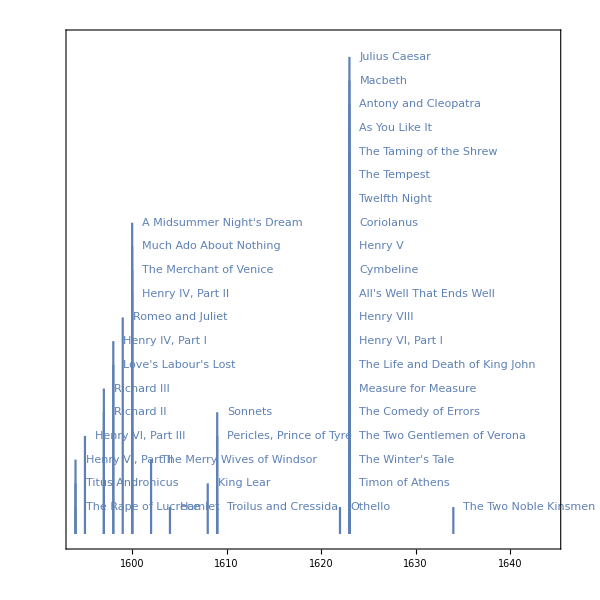

```mathematica
TimelinePlot[dateAndTitles]
```

Find out which plays were published after Shakespeare’s death:

```mathematica
Entity["Person","WilliamShakespeare::s9r82"]["DeathDate"]
```

Day: Tue 23 Apr 1616 (Juliancalendar)

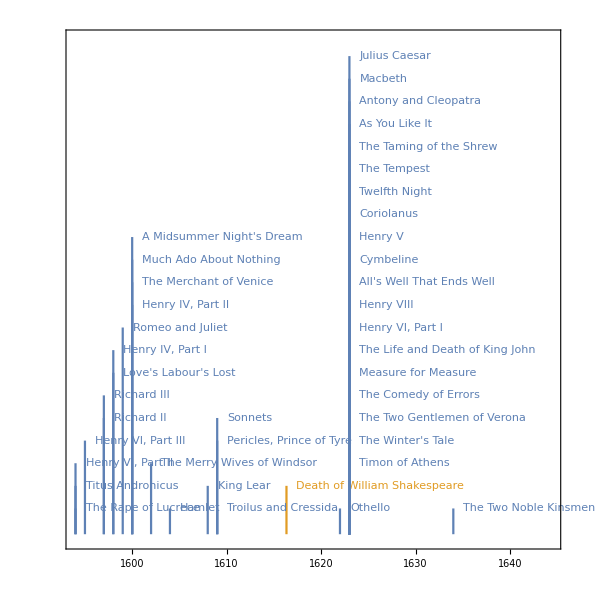

```mathematica
TimelinePlot[{dateAndTitles,Labeled[Entity["Person","WilliamShakespeare::s9r82"]["DeathDate"],"Death of William Shakespeare"]}]
```

## Using Data from the Wolfram Data Repository

### Text Analysis of Shakespeare’s Sonnets

Retrieve the ResourceObject:

```mathematica
ResourceObject["Shakespeare's Sonnets"]
```

ResourceObject[…]

View the data:

```mathematica
TextCases[ResourceData["Shakespeare's Sonnets"],"Paragraph"][[2]]
```

From fairest creatures we desire increase,
That thereby beauty's rose might never die,
But as the riper should by time decease,
His tender heir might bear his memory:
But thou contracted to thine own bright eyes,
Feed'st thy light's flame with self-substantial fuel,
Making a famine where abundance lies,
Thy self thy foe, to thy sweet self too cruel:
Thou that art now the world's fresh ornament,
And only herald to the gaudy spring,
Within thine own bud buriest thy content,
And tender churl mak'st waste in niggarding:
  Pity the world, or else this glutton be,
  To eat the world's due, by the grave and thee.

A word cloud:

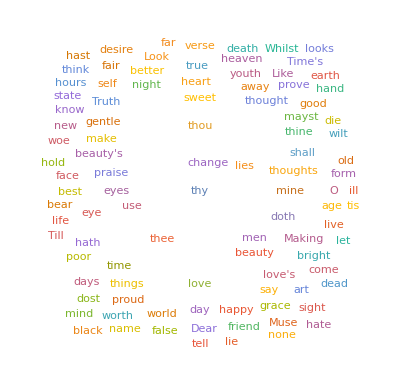

```mathematica
WordCloud[DeleteStopwords[TextCases[ResourceData["Shakespeare's Sonnets"],"Word"]]]
```

## References

Wolfram Blog post: Analyzing Shakespeare's Texts on the 400th Anniversary of His Death

Wolfram Community™ discussion: 400th Anniversary of Shakespeare's Death

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```